```mathematica
s58 = (8.8922936714104939)*Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search58\\Lambda.asc"][[2;;]];
s59 = (8.8906363348053521)*Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search59\\Lambda.asc"][[2;;]];
s60 = (8.8858345118514332)*Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search60\\Lambda.asc"][[2;;]];
s61 = (8.8775285468009351)*Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search61\\Lambda.asc"][[2;;]];
s62 = (8.8654218783351055)*Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search62\\Lambda.asc"][[2;;]];
s63 = (8.8501739990669162)*Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search63\\Lambda.asc"][[2;;]];
s55p = Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search55\\Lambda.asc"][[2;;]];
s58p = Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search58\\Lambda.asc"][[2;;]];
s59p= Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search59\\Lambda.asc"][[2;;]];
s60p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search60\\Lambda.asc"][[2;;]];
s61p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search61\\Lambda.asc"][[2;;]];
s62p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search62\\Lambda.asc"][[2;;]];
s63p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search63\\Lambda.asc"][[2;;]];
s64p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search64\\Lambda.asc"][[2;;]];
s65p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search65\\Lambda.asc"][[2;;]];
s99p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search99\\Lambda.asc"][[2;;]];
s101p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search101\\Lambda.asc"][[2;;]];
s102p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search102\\Lambda.asc"][[2;;]];
s103p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search103\\Lambda.asc"][[2;;]];
s104p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search104\\Lambda.asc"][[2;;]];
s105p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search105\\Lambda.asc"][[2;;]];
s106p =Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\search106\\Lambda.asc"][[2;;]];
```

```mathematica
sE58 = Map[Function[x,{ Re[ Exp[ x[[1]]+I x[[2]] ] ],Im[ Exp[ x[[1]]+I x[[2]] ] ] }],s58];
sE59 = Map[Function[x,{ Re[ Exp[ x[[1]]+I x[[2]] ] ],Im[ Exp[ x[[1]]+I x[[2]] ] ] }],s59];
sE60 = Map[Function[x,{ Re[ Exp[ x[[1]]+I x[[2]] ] ],Im[ Exp[ x[[1]]+I x[[2]] ] ] }],s60];
sE61 = Map[Function[x,{ Re[ Exp[ x[[1]]+I x[[2]] ] ],Im[ Exp[ x[[1]]+I x[[2]] ] ] }],s61];
sE62 = Map[Function[x,{ Re[ Exp[ x[[1]]+I x[[2]] ] ],Im[ Exp[ x[[1]]+I x[[2]] ] ] }],s62];
sE63 = Map[Function[x,{ Re[ Exp[ x[[1]]+I x[[2]] ] ],Im[ Exp[ x[[1]]+I x[[2]] ] ] }],s63];
```

```mathematica
p8 = Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\p8p32\\Lambda.asc"][[2;;]];
```

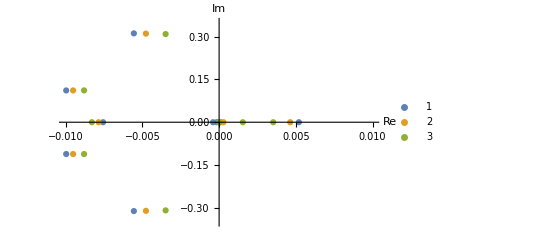

```mathematica
ListPlot[{s58p,s59p,s60p},PlotRange->{{-0.01,.01},{-0.35,0.35}},AxesLabel->{"Re","Im"},PlotLegends->Automatic]
```

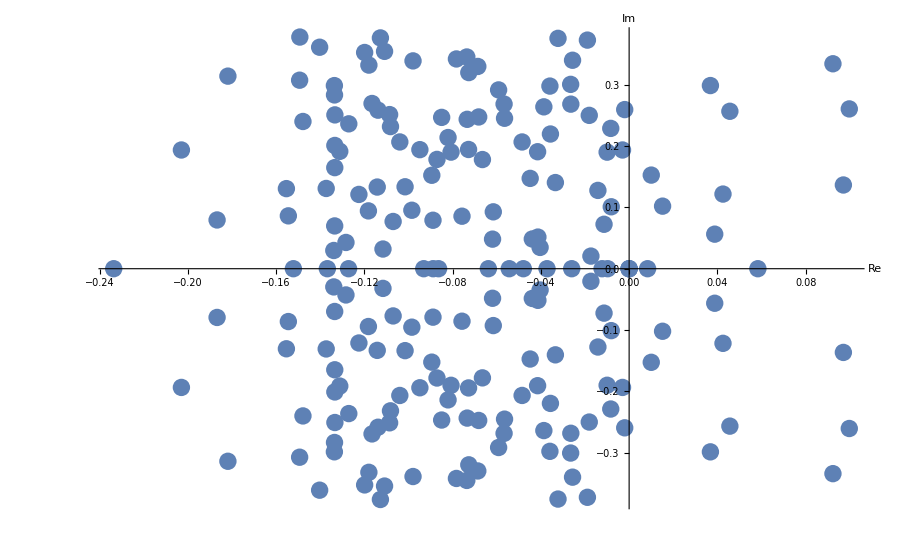

```mathematica
ListPlot[p8,AxesLabel->{"Re","Im"}]
```

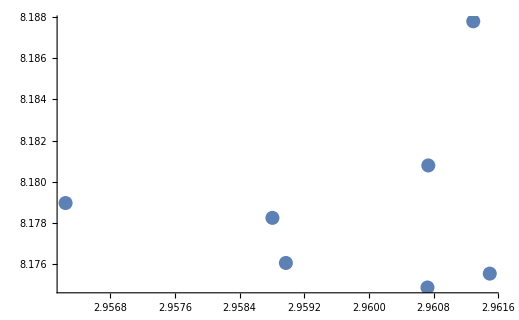

```mathematica
ListPlot[Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\second.csv"]]
```

```mathematica
Import["C:\\Users\\Varchas\\Desktop\\EigenStuff\\second.csv"]
```

{{2.95881,8.17824},{2.96074,8.18079},{2.96129,8.18779},{2.9615,8.17554},{2.96072,8.17486},{2.95897,8.17605},{2.95625,8.17896}}

```mathematica
P8 = Partition[(Import["C:\\Users\\Varchas\\Desktop\\Visuals\\p8p32.asc"]//StringSplit)[[23;;]],4]//ToExpression;
E1 = Partition[Map[Function[x,ToExpression@StringReplace[x,"e"->"*10^"]],(Import["C:\\Users\\Varchas\\Desktop\\Visuals\\Perturb off HWK 400\e1.asc" ]//StringSplit)[[23;;]]],4]//ToExpression;
```

```mathematica
ListPointPlot3D[P8[[1;;,2;;4]]]
```

-Graphics3D-

```mathematica
P8//Dimensions
```

{1000,4}

```mathematica
E1//Dimensions
```

{4999,4}

```mathematica
ListPointPlot3D[]
```

-Graphics3D-

```mathematica
Manipulate[pts = E1[[1999;;end;;delta,2;;4]];
Show[ListPointPlot3D[pts,PlotRange->Full],Graphics3D@Line@pts],{end,2000,4999,10},{delta,1,20,1}]
```

```mathematica
p1 = Show[ListPointPlot3D[pts,PlotRange->Full],Graphics3D@Line@pts]
```

-Graphics3D-

```mathematica
Image3DSlices[p1]
```

Image3DSlices::arg1: Expecting Image or Image3D instead of ….

Image3DSlices[-Graphics3D-]

```mathematica
Manipulate[pts = E1[[1;;end;;delta,2;;4]];
pts2 =pts;
pts3 = Table[If[Abs[pts2[[i,2]] - 0.26] < 0.001 && pts2[[i,1]] >- 0.088,{pts2[[i,1]],pts2[[i,3]]}],{i,1,Length[pts2]}];
pts4 = Select[pts3,UnsameQ[#,Null]&];
Show[ListPlot[pts4,PlotRange->Full],Graphics@Line@pts4],{end,1,4999,10},{delta,1,20,1}]
```

-Graphics3D-

```mathematica
Dimensions[pts3]
```

{841}

```mathematica
pts2[[1]]
```

{-0.0907322,0.28036,0.254212}